```mathematica
Play[Sin[256*2 π t]+Sin[1.25*256*2 π t]+Sin[1.5*256*2 π t]+Sin[2*256*2 π t],{t,0,1}]
```

-Graphics-

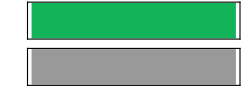

```mathematica
gE2=Sound[SoundNote["E2",5,"Guitar"]]
```

```mathematica
AudioPitchShift[gE2,2]
```

```mathematica
Manipulate[EmitSound[Sound[SoundNote[n,3]]],{n,1,10,1}]
```

```mathematica
Play[Sin[261.626 2π t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sin[293.665 2π t],{t,0,1}]
```

-Graphics-

```mathematica
sound=Play[Sin[16.351 2π t],{t,0,1}]
```

-Graphics-

```mathematica
Export["c0.mp3",sound]
```

c0.mp3

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["c0.mp3"]]]
```

```mathematica
EmitSound[%336]
```

```mathematica
LinkCreate[]
```

LinkObject[…]

```mathematica
LinkReadyQ[LinkObject[…]]
```

False